# Omicron analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries

```mathematica
dataset="omicron-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=300;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-01

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2021-12-13

```mathematica
countries=Union[seqData[[All,2]]]
```

{Australia,Canada,Denmark,France,Germany,Ireland,Israel,Netherlands,Norway,South Africa,Spain,Sweden,Switzerland,United Kingdom,USA}

```mathematica
countries=Complement[countries,countriesToDrop]
```

{Australia,Canada,Denmark,France,Germany,Ireland,Israel,Netherlands,Norway,South Africa,Spain,Sweden,Switzerland,United Kingdom,USA}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-15;;-1]]&,countries]
```

{Australia→{{2021-11-29,217},{2021-11-30,164},{2021-12-01,189},{2021-12-02,172},{2021-12-03,206},{2021-12-04,182},{2021-12-05,191},{2021-12-06,313},{2021-12-07,209},{2021-12-08,165},{2021-12-09,228},{2021-12-10,119},{2021-12-11,70},{2021-12-12,173},{2021-12-13,24}},Canada→{{2021-11-29,590},{2021-11-30,542},{2021-12-01,505},{2021-12-02,303},{2021-12-03,115},{2021-12-04,170},{2021-12-05,93},{2021-12-06,189},{2021-12-07,118},{2021-12-08,160},{2021-12-09,144},{2021-12-10,52},{2021-12-11,29},{2021-12-12,0},{2021-12-13,0}},Denmark→{{2021-11-29,1827},{2021-11-30,1634},{2021-12-01,2331},{2021-12-02,2698},{2021-12-03,2381},{2021-12-04,2924},{2021-12-05,3457},{2021-12-06,4231},{2021-12-07,1518},{2021-12-08,1259},{2021-12-09,434},{2021-12-10,629},{2021-12-11,540},{2021-12-12,251},{2021-12-13,439}},France→{{2021-11-29,3066},{2021-11-30,309},{2021-12-01,140},{2021-12-02,171},{2021-12-03,206},{2021-12-04,103},{2021-12-05,128},{2021-12-06,1383},{2021-12-07,175},{2021-12-08,105},{2021-12-09,61},{2021-12-10,46},{2021-12-11,24},{2021-12-12,0},{2021-12-13,0}},Germany→{{2021-11-29,2536},{2021-11-30,2137},{2021-12-01,1311},{2021-12-02,1489},{2021-12-03,1235},{2021-12-04,1053},{2021-12-05,270},{2021-12-06,1717},{2021-12-07,1047},{2021-12-08,409},{2021-12-09,1329},{2021-12-10,747},{2021-12-11,318},{2021-12-12,40},{2021-12-13,16}},Ireland→{{2021-11-29,41},{2021-11-30,675},{2021-12-01,23},{2021-12-02,7},{2021-12-03,3},{2021-12-04,2},{2021-12-05,7},{2021-12-06,2},{2021-12-07,19},{2021-12-08,2},{2021-12-09,0},{2021-12-10,6},{2021-12-11,53},{2021-12-12,0},{2021-12-13,0}},Israel→{{2021-11-29,217},{2021-11-30,223},{2021-12-01,224},{2021-12-02,232},{2021-12-03,154},{2021-12-04,208},{2021-12-05,254},{2021-12-06,200},{2021-12-07,222},{2021-12-08,137},{2021-12-09,36},{2021-12-10,0},{2021-12-11,0},{2021-12-12,0},{2021-12-13,0}},Netherlands→{{2021-11-29,206},{2021-11-30,177},{2021-12-01,217},{2021-12-02,223},{2021-12-03,171},{2021-12-04,131},{2021-12-05,186},{2021-12-06,106},{2021-12-07,48},{2021-12-08,49},{2021-12-09,94},{2021-12-10,31},{2021-12-11,16},{2021-12-12,0},{2021-12-13,0}},Norway→{{2021-11-29,133},{2021-11-30,73},{2021-12-01,70},{2021-12-02,58},{2021-12-03,76},{2021-12-04,44},{2021-12-05,43},{2021-12-06,63},{2021-12-07,34},{2021-12-08,17},{2021-12-09,11},{2021-12-10,10},{2021-12-11,7},{2021-12-12,0},{2021-12-13,0}},South Africa→{{2021-11-29,139},{2021-11-30,145},{2021-12-01,118},{2021-12-02,85},{2021-12-03,71},{2021-12-04,22},{2021-12-05,9},{2021-12-06,58},{2021-12-07,41},{2021-12-08,20},{2021-12-09,52},{2021-12-10,53},{2021-12-11,21},{2021-12-12,0},{2021-12-13,0}},Spain→{{2021-11-29,106},{2021-11-30,131},{2021-12-01,214},{2021-12-02,112},{2021-12-03,199},{2021-12-04,64},{2021-12-05,35},{2021-12-06,31},{2021-12-07,100},{2021-12-08,92},{2021-12-09,65},{2021-12-10,88},{2021-12-11,53},{2021-12-12,0},{2021-12-13,0}},Sweden→{{2021-11-29,530},{2021-11-30,408},{2021-12-01,392},{2021-12-02,428},{2021-12-03,240},{2021-12-04,97},{2021-12-05,66},{2021-12-06,146},{2021-12-07,108},{2021-12-08,107},{2021-12-09,96},{2021-12-10,78},{2021-12-11,66},{2021-12-12,0},{2021-12-13,0}},Switzerland→{{2021-11-29,772},{2021-11-30,841},{2021-12-01,309},{2021-12-02,182},{2021-12-03,465},{2021-12-04,443},{2021-12-05,166},{2021-12-06,351},{2021-12-07,216},{2021-12-08,115},{2021-12-09,118},{2021-12-10,79},{2021-12-11,78},{2021-12-12,0},{2021-12-13,0}},United Kingdom→{{2021-11-29,12546},{2021-11-30,11033},{2021-12-01,8854},{2021-12-02,7384},{2021-12-03,6624},{2021-12-04,5918},{2021-12-05,6839},{2021-12-06,9699},{2021-12-07,10427},{2021-12-08,8001},{2021-12-09,6410},{2021-12-10,6191},{2021-12-11,4198},{2021-12-12,5393},{2021-12-13,3735}},USA→{{2021-11-29,8827},{2021-11-30,7548},{2021-12-01,6661},{2021-12-02,5634},{2021-12-03,4463},{2021-12-04,2553},{2021-12-05,1366},{2021-12-06,4234},{2021-12-07,2504},{2021-12-08,2542},{2021-12-09,1918},{2021-12-10,1596},{2021-12-11,813},{2021-12-12,0},{2021-12-13,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text[label<>" = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountries=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
legendsForCountries=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForCountries];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft},panels],3],Spacings->{0,0},Alignment->Right]
```

|  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft},panels],3],Spacings->{0,0},Alignment->Right]
```

|  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-countries_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

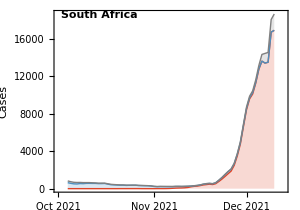

```mathematica
splitCasePlot["South Africa"]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

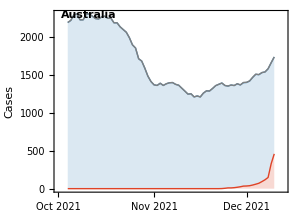
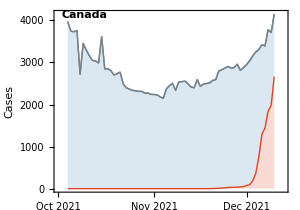
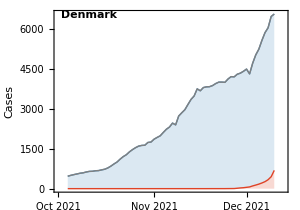
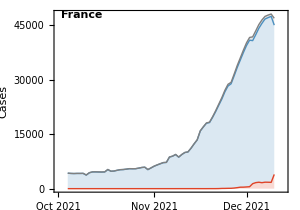
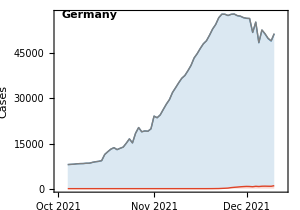
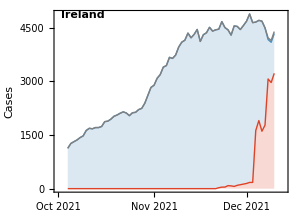
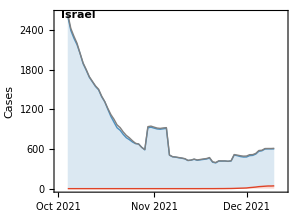
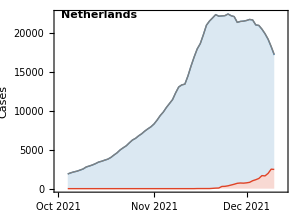
|  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft},panels],3],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=30000;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{8,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{8,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{8,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text[label<>" r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForCountries=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,countries];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{countries,legendsForCountries}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft},panels],3],Spacings->{0,0},Alignment->Right]
```

|  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-log-cases.png

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/omicron-countries_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2021-12-21

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.001];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,6]},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;3]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryRtPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

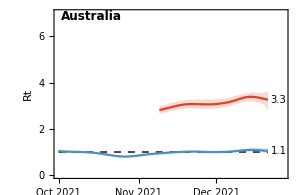
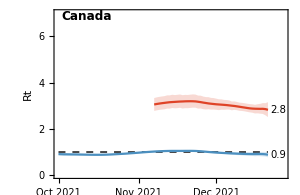
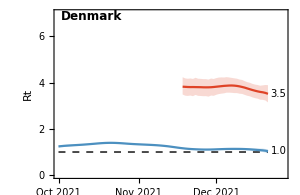
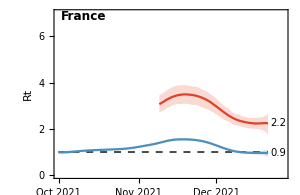
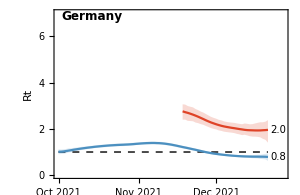
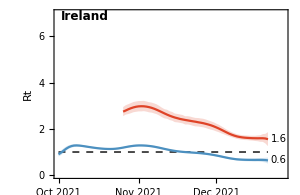
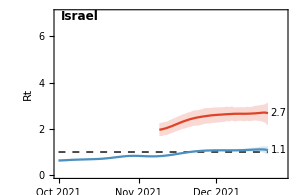
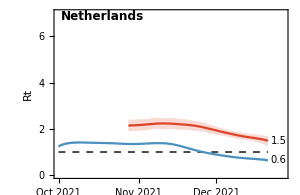
|  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft},panels],3],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron"][[-1,1]],Round[rtGather[#,"Omicron"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron"][[-1,2]],0.1]}&,countries]
```

{Australia→{2021-12-21,3.3,2.8,3.6},Canada→{2021-12-21,2.8,2.5,3.1},Denmark→{2021-12-21,3.5,3.1,3.9},France→{2021-12-21,2.2,1.8,2.6},Germany→{2021-12-21,2.,1.4,2.4},Ireland→{2021-12-21,1.6,1.3,1.9},Israel→{2021-12-21,2.7,2.1,3.1},Netherlands→{2021-12-21,1.5,1.2,1.7},Norway→{2021-12-21,1.1,0.7,1.4},South Africa→{2021-12-21,0.9,0.5,1.2},Spain→{2021-12-21,3.2,2.4,3.9},Sweden→{2021-12-21,2.5,1.9,2.9},Switzerland→{2021-12-21,1.8,1.4,2.2},United Kingdom→{2021-12-21,1.5,1.1,1.9},USA→{2021-12-21,3.4,2.8,3.9}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/omicron-countries_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.001];
```

```mathematica
rData=DeleteCases[rData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.35}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,9]},
{-0.35,0.35}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;3]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryLittleRPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

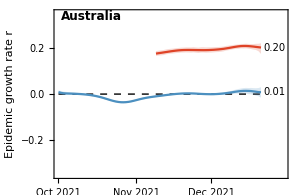
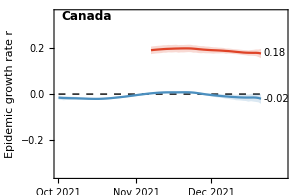
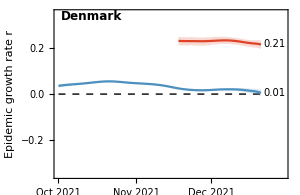
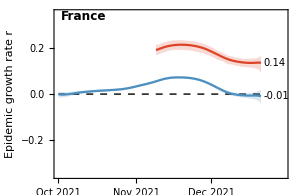
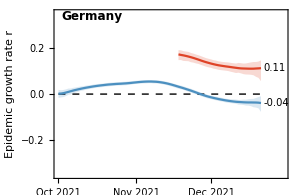
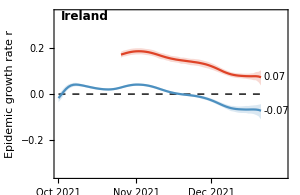
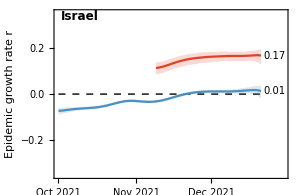
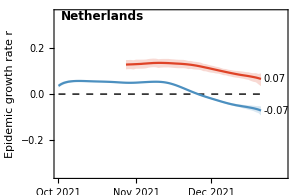
|  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft},panels],3],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[rGather[#,"Omicron"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,countries]
```

{Australia→{2021-12-21,0.2,0.17,0.22},Canada→{2021-12-21,0.18,0.15,0.19},Denmark→{2021-12-21,0.21,0.19,0.23},France→{2021-12-21,0.14,0.09,0.16},Germany→{2021-12-21,0.11,0.06,0.15},Ireland→{2021-12-21,0.07,0.04,0.1},Israel→{2021-12-21,0.17,0.13,0.19},Netherlands→{2021-12-21,0.07,0.03,0.09},Norway→{2021-12-21,0.02,-0.05,0.06},South Africa→{2021-12-21,-0.03,-0.11,0.03},Spain→{2021-12-21,0.2,0.15,0.23},Sweden→{2021-12-21,0.16,0.11,0.18},Switzerland→{2021-12-21,0.1,0.06,0.13},United Kingdom→{2021-12-21,0.06,0.01,0.11},USA→{2021-12-21,0.21,0.17,0.23}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[Log[2]/rGather[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron"][[-1,2]],0.1]}&,countries]
```

{Australia→{2021-12-21,3.4,3.2,4.},Canada→{2021-12-21,4.,3.6,4.5},Denmark→{2021-12-21,3.2,3.,3.6},France→{2021-12-21,5.1,4.2,7.4},Germany→{2021-12-21,6.2,4.8,12.4},Ireland→{2021-12-21,9.5,6.7,18.7},Israel→{2021-12-21,4.2,3.6,5.5},Netherlands→{2021-12-21,10.6,7.8,20.3},Norway→{2021-12-21,43.9,11.5,-14.9},South Africa→{2021-12-21,-27.3,26.5,-6.4},Spain→{2021-12-21,3.5,3.,4.7},Sweden→{2021-12-21,4.5,3.8,6.4},Switzerland→{2021-12-21,6.8,5.2,12.5},United Kingdom→{2021-12-21,10.7,6.5,61.6},USA→{2021-12-21,3.3,3.,4.}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/omicron-countries_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{8,240000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

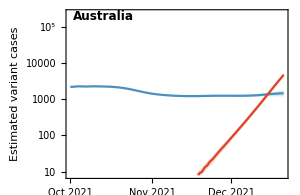
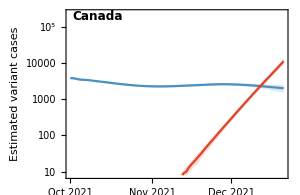
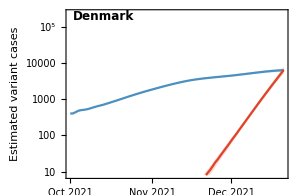
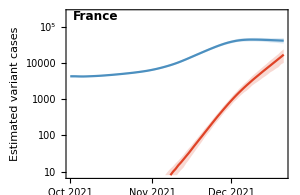
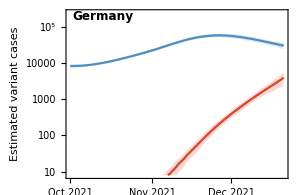
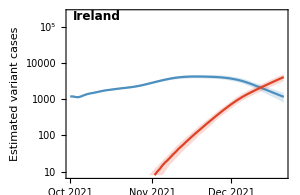
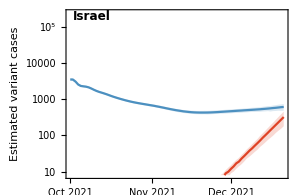
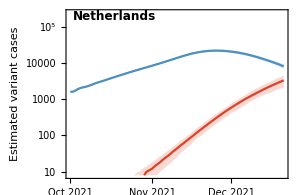
|  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft},panels],3],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

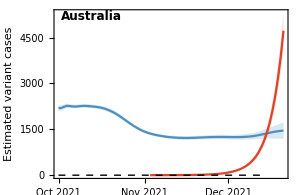
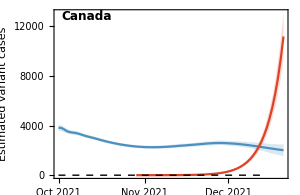
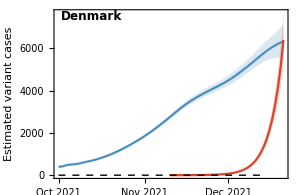
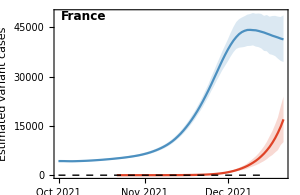
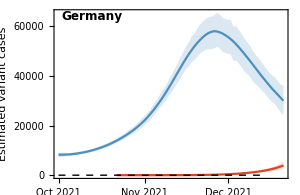
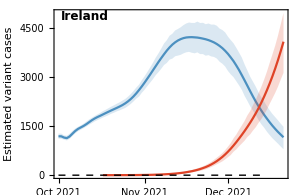
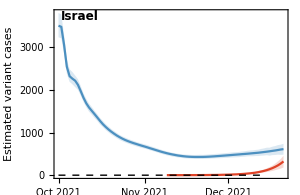
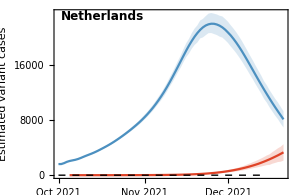
|  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft},panels],3],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron"][[-1,1]],Round[pGather[#,"Omicron"][[-1,2]]],Round[pGatherLower[#,"Omicron"][[-1,2]]],Round[pGatherUpper[#,"Omicron"][[-1,2]]]}&,countries]
```

{Australia→{2021-12-21,4723,4093,5304},Canada→{2021-12-21,11182,9261,13076},Denmark→{2021-12-21,6402,5079,7673},France→{2021-12-21,17009,10069,23926},Germany→{2021-12-21,3932,2400,5463},Ireland→{2021-12-21,4089,3131,4968},Israel→{2021-12-21,322,179,456},Netherlands→{2021-12-21,3303,2110,4472},Norway→{2021-12-21,4298,3432,5094},South Africa→{2021-12-21,20696,16288,25196},Spain→{2021-12-21,32543,21765,42689},Sweden→{2021-12-21,2828,2117,3454},Switzerland→{2021-12-21,2032,1193,2812},United Kingdom→{2021-12-21,77154,67444,87355},USA→{2021-12-21,73141,53933,95084}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[country_,variant_]:=Module[{popSize},
popSize=QuantityMagnitude[CountryData[country,"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[country,variant]]
]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairs},
pairs=phaseGather[country,"Omicron"];
ListLogLinearPlot[{pairs,{Last[pairs]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{0,100},
{-0.1,0.35}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->colors[[3]],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,countries];
```

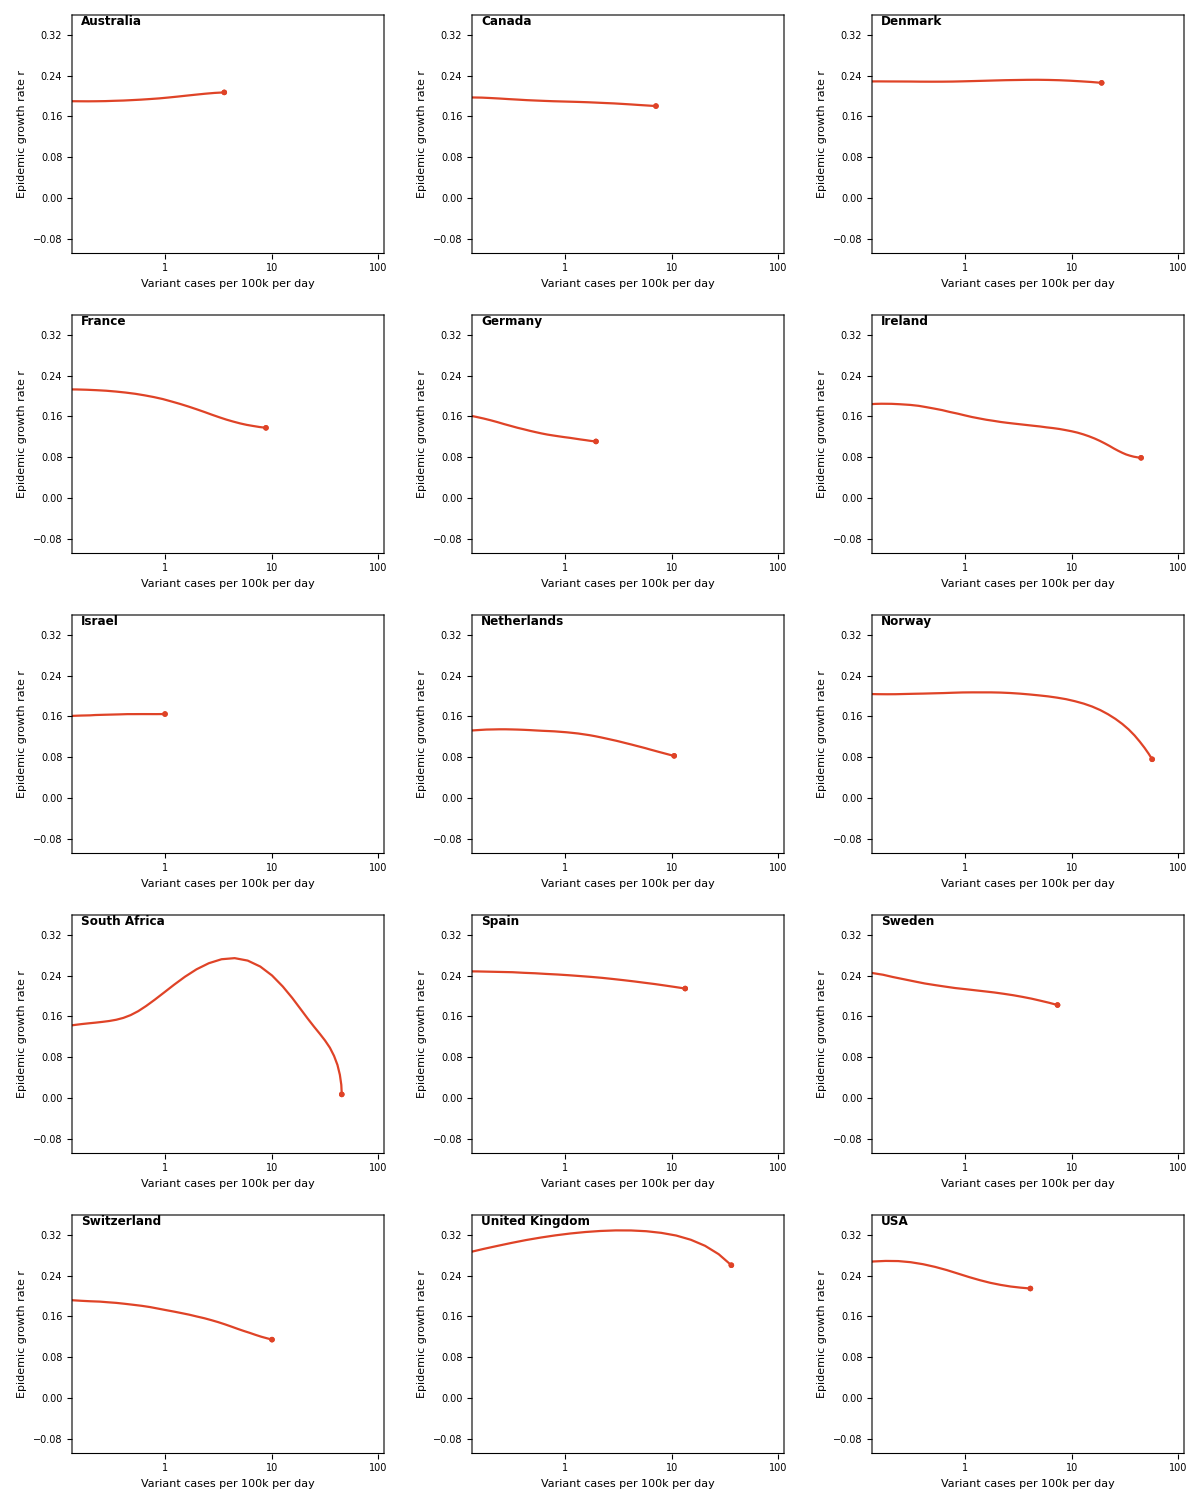

```mathematica
fig=Grid[gappedPartition[panels,3],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-cases-vs-rt.png

## Comparison to vaccination rate

Country-level vaccination data is obtained from Our World in Data, following instructions at https://github.com/owid/covid-19-data/blob/master/public/data/README.md

The full CSV is available at: https://covid.ourworldindata.org/data/owid-covid-data.csv

```mathematica
comparisonDate=endDate
```

2021-12-13

### Data

```mathematica
vData=Import["https://covid.ourworldindata.org/data/owid-covid-data.csv","CSV"];
```

```mathematica
Dimensions[vData]
```

{149029,67}

```mathematica
header=First[vData]
```

{iso_code,continent,location,date,total_cases,new_cases,new_cases_smoothed,total_deaths,new_deaths,new_deaths_smoothed,total_cases_per_million,new_cases_per_million,new_cases_smoothed_per_million,total_deaths_per_million,new_deaths_per_million,new_deaths_smoothed_per_million,reproduction_rate,icu_patients,icu_patients_per_million,hosp_patients,hosp_patients_per_million,weekly_icu_admissions,weekly_icu_admissions_per_million,weekly_hosp_admissions,weekly_hosp_admissions_per_million,new_tests,total_tests,total_tests_per_thousand,new_tests_per_thousand,new_tests_smoothed,new_tests_smoothed_per_thousand,positive_rate,tests_per_case,tests_units,total_vaccinations,people_vaccinated,people_fully_vaccinated,total_boosters,new_vaccinations,new_vaccinations_smoothed,total_vaccinations_per_hundred,people_vaccinated_per_hundred,people_fully_vaccinated_per_hundred,total_boosters_per_hundred,new_vaccinations_smoothed_per_million,new_people_vaccinated_smoothed,new_people_vaccinated_smoothed_per_hundred,stringency_index,population,population_density,median_age,aged_65_older,aged_70_older,gdp_per_capita,extreme_poverty,cardiovasc_death_rate,diabetes_prevalence,female_smokers,male_smokers,handwashing_facilities,hospital_beds_per_thousand,life_expectancy,human_development_index,excess_mortality_cumulative_absolute,excess_mortality_cumulative,excess_mortality,excess_mortality_cumulative_per_million}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{iso_code→1,continent→2,location→3,date→4,total_cases→5,new_cases→6,new_cases_smoothed→7,total_deaths→8,new_deaths→9,new_deaths_smoothed→10,total_cases_per_million→11,new_cases_per_million→12,new_cases_smoothed_per_million→13,total_deaths_per_million→14,new_deaths_per_million→15,new_deaths_smoothed_per_million→16,reproduction_rate→17,icu_patients→18,icu_patients_per_million→19,hosp_patients→20,hosp_patients_per_million→21,weekly_icu_admissions→22,weekly_icu_admissions_per_million→23,weekly_hosp_admissions→24,weekly_hosp_admissions_per_million→25,new_tests→26,total_tests→27,total_tests_per_thousand→28,new_tests_per_thousand→29,new_tests_smoothed→30,new_tests_smoothed_per_thousand→31,positive_rate→32,tests_per_case→33,tests_units→34,total_vaccinations→35,people_vaccinated→36,people_fully_vaccinated→37,total_boosters→38,new_vaccinations→39,new_vaccinations_smoothed→40,total_vaccinations_per_hundred→41,people_vaccinated_per_hundred→42,people_fully_vaccinated_per_hundred→43,total_boosters_per_hundred→44,new_vaccinations_smoothed_per_million→45,new_people_vaccinated_smoothed→46,new_people_vaccinated_smoothed_per_hundred→47,stringency_index→48,population→49,population_density→50,median_age→51,aged_65_older→52,aged_70_older→53,gdp_per_capita→54,extreme_poverty→55,cardiovasc_death_rate→56,diabetes_prevalence→57,female_smokers→58,male_smokers→59,handwashing_facilities→60,hospital_beds_per_thousand→61,life_expectancy→62,human_development_index→63,excess_mortality_cumulative_absolute→64,excess_mortality_cumulative→65,excess_mortality→66,excess_mortality_cumulative_per_million→67}

```mathematica
vData=Drop[vData,1];
```

```mathematica
Length[vData]
```

149028

Replace “United States” with “USA”

```mathematica
vData=Map[Join[#[[1;;2]],{If[#[[3]]=="United States","USA",#[[3]]]},#[[4;;-1]]]&,vData];
```

Remove lines lacking data

```mathematica
vData=DeleteCases[vData,x_/;x[[43]]==""];
```

```mathematica
vData=DeleteCases[vData,x_/;x[[44]]==""];
```

```mathematica
fullyVacGather[country_]:=Module[{series},
series=Cases[vData,x_/;x[[3]]==country&&x[[4]]==comparisonDate];
If[Length[series]>0,series[[1,43]],Null]
]
```

```mathematica
fullyVacGather["United Kingdom"]
```

68.62

```mathematica
fullyVacGather["Netherlands"]
```

```mathematica
boosterGather[country_]:=Module[{series},
series=Cases[vData,x_/;x[[3]]==country&&x[[4]]==comparisonDate];
If[Length[series]>0,series[[1,44]],Null]
]
```

```mathematica
boosterGather["United Kingdom"]
```

35.3

```mathematica
totalCasesGather[country_]:=Module[{series},
series=Cases[vData,x_/;x[[3]]==country&&x[[4]]==comparisonDate];
If[Length[series]>0,100*series[[1,11]]/1000000,Null]
]
```

```mathematica
totalCasesGather["USA"]
```

15.0556

```mathematica
series=DeleteCases[Table[{country,FirstCase[rGather[country,"Omicron"],x_/;x[[1]]==comparisonDate][[2]],fullyVacGather[country],boosterGather[country],totalCasesGather[country]},{country,countries}],x_/;x[[3]]==Null||x[[4]]==Null]
```

{{Australia,0.207131,74.95,2.99,0.902497},{Canada,0.180301,76.75,7.96,4.85911},{Denmark,0.225841,77.39,23.19,9.67072},{France,0.137583,71.25,20.98,12.3076},{Germany,0.110861,69.05,24.91,7.84433},{Ireland,0.0787475,76.58,25.25,12.6092},{Israel,0.164647,62.37,44.47,14.5411},{Norway,0.0758828,71.02,18.68,5.81598},{Spain,0.214706,80.74,19.7,11.4236},{Switzerland,0.114448,66.17,13.81,13.0269},{United Kingdom,0.26045,68.62,35.3,15.9716},{USA,0.214737,60.83,17.29,15.0556}}

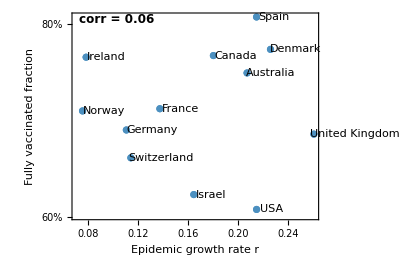

```mathematica
fig=ListPlot[Map[{#}&,series[[All,{2,3}]]],PlotLabels->Placed[series[[All,1]],Right],PlotStyle->colors[[2]],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Epidemic growth rate r","Fully vaccinated fraction"},FrameTicks->{{Table[{i,ToString[i]<>"%"},{i,0,100,5}],Automatic},{Automatic,Automatic}},PlotRangePadding->{{Scaled[0.02],Scaled[0.18]},{Scaled[0.03],Scaled[0.05]}},AspectRatio->0.65,Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[series[[All,2]],series[[All,3]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

```mathematica
Export["figures/"<>dataset<>"_r-vs-vaccinated-fraction.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_r-vs-vaccinated-fraction.png

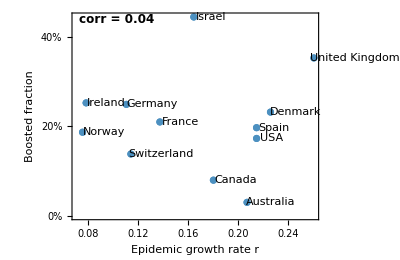

```mathematica
fig=ListPlot[Map[{#}&,series[[All,{2,4}]]],PlotLabels->Placed[series[[All,1]],Right],PlotStyle->colors[[2]],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Epidemic growth rate r","Boosted fraction"},FrameTicks->{{Table[{i,ToString[i]<>"%"},{i,0,100,5}],Automatic},{Automatic,Automatic}},PlotRangePadding->{{Scaled[0.02],Scaled[0.18]},{Scaled[0.03],Scaled[0.05]}},AspectRatio->0.65,Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[series[[All,2]],series[[All,4]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

```mathematica
Export["figures/"<>dataset<>"_r-vs-boosted-fraction.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_r-vs-boosted-fraction.png

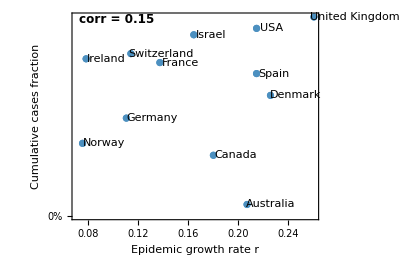

```mathematica
fig=ListPlot[Map[{#}&,series[[All,{2,5}]]],PlotLabels->Placed[series[[All,1]],Right],PlotStyle->colors[[2]],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Epidemic growth rate r","Cumulative cases fraction"},FrameTicks->{{Table[{i,ToString[i]<>"%"},{i,0,100,5}],Automatic},{Automatic,Automatic}},PlotRangePadding->{{Scaled[0.02],Scaled[0.18]},{Scaled[0.03],Scaled[0.05]}},AspectRatio->0.65,Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[series[[All,2]],series[[All,5]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

```mathematica
Export["figures/"<>dataset<>"_r-vs-infected-fraction.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_r-vs-infected-fraction.png